```mathematica
Zip[a_,b_]:=Module[{i, output},
output={};
For[i=1,i≤Length[a],i++,
AppendTo[output,{a[[i]],b[[i]]}];
];
Return[output];
];
```

```mathematica
roots[f_,x_,sdom_:True]:=Module[{i,rawSol,root,output},
rawSol=Solve[f==0&&sdom,x,Reals];
root={};
output={};
For[i=1,i≤Length[rawSol],i++,
If[rawSol[[i,1,2,0]]==Root,
AppendTo[root,N[rawSol[[i]],2]];
Continue[];
];
AppendTo[root,rawSol[[i]]];
];
If[Or[root=={{}},root=={}],
Return[{}],
For[i=1,i≤Length[root],i++,
AppendTo[output, {root[[i,1,2]],0}];
];
Return[output]
];
];
```

```mathematica
approximateRoots[solutions_]:=Module[{i, output},
output={};
For[i=1,i≤Length[solutions],i++,
If[solutions[[i,1,2,0]]==Root,
AppendTo[output, N[solutions[[i]],2]];
Continue[];
];
AppendTo[output, solutions[[i]]];
];
Return[output];
];
```

```mathematica
turningPoints[f_,x_,sdom_:True]:=Module[{solveResult,skippedIfStatment},
skippedIfStatment=True;
If[D[f,x]==0,
skippedIfStatment=False;
solveResult={{}};
];
If[skippedIfStatment,
solveResult=approximateRoots[Solve[D[f,x]==0&&sdom,x,Reals]];
];
If[Or[solveResult=={{}},solveResult=={}],
Return[{}]
,
Return[Zip[solveResult[[All,1,2]],f/.x->solveResult[[All,1,2]]]]
];
Print["The answer is liable to contain errors"];
Return[{}]
];
```

```mathematica
maximumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])<0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
```

```mathematica
minimumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])>0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
```

```mathematica
ClearAll[pointsOfInflection]
```

```mathematica
pointsOfInflection[f_,x_,sdom_:True,highestOrder_:50]:=Module[{i,j,skippedIfStatment,secondDSolutions,output},
output={};
skippedIfStatment=False;
If[D[f,{x,2}]==0,Return[{}]];
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]][[All,1,2]];
For[j=1,j≤Length[secondDSolutions],j++,
i=3;
While[True,
If[i>highestOrder,Return[{}]];
If[(D[f,{x,i}]/.x->secondDSolutions[[j]])==0,
i ++;
Continue[];
];
Break[];
];
If[OddQ[i],
AppendTo[output,secondDSolutions[[j]]];
];
];
Return[Zip[output,f/.x->output]];
];
```

```mathematica
pointsOfInflection[x^7+x+x^2,x]
```

{{-0.54,-0.3}}

```mathematica
stationaryPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,POIs,firstDSolutions,output},
output={};
POIs=pointsOfInflection[f,x,sdom][[All,1]];
firstDSolutions=approximateRoots[Solve[D[f,x]==0&&sdom,x,Reals]][[All,1,2]];
For[i=1,i≤Length[POIs],i++,
For[j=1,j≤Length[firstDSolutions],j++,
If[POIs[[i]]==firstDSolutions[[j]],
AppendTo[output,POIs[[i]]];
Break[];
];
];
];
Return[Zip[output,f/.x->output]];
];
```

```mathematica
stationaryPointsOfInflection[x^7,x]
```

{{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
movingPointsOfInflection[x^3,x]
```

{}

```mathematica
ClearAll[movingPointsOfInflection];
```

```mathematica
movingPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,POIs,firstDSolutions,output,shouldAdd},
output={};
POIs=pointsOfInflection[f,x,sdom][[All,1]];
firstDSolutions=approximateRoots[Solve[D[f,x]==0&&sdom,x,Reals]][[All,1,2]];
For[i=1,i≤Length[POIs],i++,
shouldAdd=True;
For[j=1,j≤Length[firstDSolutions],j++,
If[POIs[[i]]==firstDSolutions[[j]],
shouldAdd=False;
];
];
If[shouldAdd,
AppendTo[output,POIs[[i]]];
];
];
Return[Zip[output,f/.x->output]];
];
```

```mathematica
concaviteAtPointAsInteger[f_,x_,p_]:=Module[{secondD},
secondD=D[f,{x,2}];
If[(secondD/.x->p)≤0,
Return[1]
,
Return[-1]
];
Return["Error"];
];
```

```mathematica
yIntercepts[f_,x_,sdom_:True]:=Module[{},
If[(f&&sdom/.x->0)==False,
Return[{}];
];
Return[{{0,(f&&sdom/.x->0)}}];
];
```

```mathematica
evalulateValue[val_]:=val
```

```mathematica
plotColors[n_]:=ColorData[97,"ColorList"][[Mod[n,15]]]
```

```mathematica
plotinator[f_,dom_,showObliqueAsymptotes_:False]:=Module[{i,j,keyPoints,plot,absoluteRange,epilogPoints,epologTextOffset,epilogs,hAsymptotes,vAsymptotes,oAsymptotes,asymptotes,solveDomain,plotEquasions,oAsymptoteHolder,plotStyle,pointObjects,numberOfEquasions,temp,pointTypes},
keyPoints={};
plot=0;
absoluteRange=0;
epilogPoints=0;
epologTextOffset=0;
epilogs={};
solveDomain=dom[[2]]≤dom[[1]]≤dom[[3]];
plotEquasions={f};
oAsymptoteHolder={};
plotStyle={};
pointObjects={};
numberOfEquasions=0;
pointTypes={};

If[(f)[[0]]==List,
plotEquasions=f;
];

For[i=1,i≤Length[plotEquasions],i++,
AppendTo[plotStyle,{plotColors[i]}]
];
For[i=1,i≤Length[plotEquasions],i++,
temp=movingPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain];
keyPoints=Join[keyPoints,temp];
pointTypes=Join[pointTypes,Zip[temp,ConstantArray[mPOI,Length[temp]]]];
temp=stationaryPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain];
keyPoints=Join[keyPoints,temp];
pointTypes=Join[pointTypes,Zip[temp,ConstantArray[sPOI,Length[temp]]]];
temp=turningPoints[plotEquasions[[i]],dom[[1]],solveDomain];
keyPoints=Join[keyPoints,temp];
pointTypes=Join[pointTypes,Zip[temp,ConstantArray[TP,Length[temp]]]];
temp=roots[plotEquasions[[i]],dom[[1]],solveDomain];
keyPoints=Join[keyPoints,temp];
pointTypes=Join[pointTypes,Zip[temp,ConstantArray[xInt,Length[temp]]]];
temp=yIntercepts[plotEquasions[[i]],dom[[1]],solveDomain];
keyPoints=Join[keyPoints,temp];
pointTypes=Join[pointTypes,Zip[temp,ConstantArray[yInt,Length[temp]]]];
];
keyPoints=DeleteDuplicates[keyPoints];

plot=Plot[f,dom];
absoluteRange=Abs[PlotRange[plot][[2,2]]-PlotRange[plot][[2,1]]];
For[j=1,j≤Length[plotEquasions],j++,
For[i=1,i≤Length[keyPoints],i++,
epologTextOffset=1/10*absoluteRange*concaviteAtPointAsInteger[plotEquasions[[j]],dom[[1]],keyPoints[[i,1]]];
AppendTo[epilogs,Text[keyPoints[[i]],{keyPoints[[i,1]],keyPoints[[i,2]]+epologTextOffset}]];
];
];

asymptotes={};
For[j=1,j≤Length[plotEquasions],j++,
hAsymptotes=horizontalAsymptotes[plotEquasions[[j]],dom[[1]]];
vAsymptotes=verticleAsymptotes[plotEquasions[[j]],dom[[1]]];
oAsymptotes=obliqueAsymptote[plotEquasions[[j]],dom[[1]]];
For[i=1,i≤Length[hAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{dom[[2]],hAsymptotes[[i]]},{dom[[3]],hAsymptotes[[i]]}}],y==hAsymptotes[[i]]]];
];
For[i=1,i≤Length[vAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{vAsymptotes[[i]],PlotRange[plot][[2,1]]},{vAsymptotes[[i]],PlotRange[plot][[2,2]]}}],x==vAsymptotes[[i]]]];
];
For[i=1,i≤Length[oAsymptotes],i++,
AppendTo[oAsymptoteHolder,oAsymptotes[[i]]];
];
];

If[showObliqueAsymptotes,
Print["showing oblique asymptotes"];
oAsymptoteHolder=DeleteDuplicates[oAsymptoteHolder];
For[i=1,i≤Length[oAsymptoteHolder],i++,
AppendTo[plotEquasions,oAsymptoteHolder[[i]]];
];

For[i=1,i≤(Length[oAsymptoteHolder]),i++,
AppendTo[plotStyle,{Red,Dashed}];
];
];

pointTypes=DeleteDuplicates[pointTypes];
For[i=1,i≤Length[keyPoints],i++,
temp="";
For[j=1,j≤Length[pointTypes],j++,
If[keyPoints[[i]]==pointTypes[[j,1]],
If[StringLength[temp]==0,
temp=temp<>ToString[pointTypes[[j,2]]];
,
temp=temp<>","<>ToString[pointTypes[[j,2]]];
];
];
];
AppendTo[pointObjects,Tooltip[Point[keyPoints[[i]]],temp[keyPoints[[i,1]],keyPoints[[i,2]]]]];
];

plot=Plot[plotEquasions,dom,Epilog->{PointSize[Large],pointObjects,(*epilogs,*)Directive[Red,Dashed],asymptotes},PlotStyle->plotStyle,PlotLegends->"Expressions"];
Return[plot];
];
```

{{0.089,0.91},{1.5,7.},{0.59,0},{0,1},{3/2,0},{0,-3/2}}

{{{0.089,0.91},mPOI},{{1.5,7.},TP},{{0.59,0},xInt},{{0,1},yInt},{{3/2,0},xInt},{{0,-3/2},yInt}}

mPOI

TP

xInt

yInt

xInt

yInt

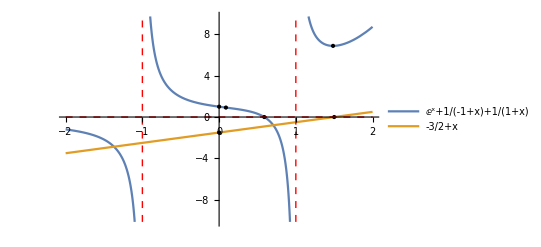

```mathematica
plotinator[{ⅇ^x+1/(x-1)+1/(x+1),x-3/2},{x,-2,2}]
```

{{1,-1/30},{0,0},{4/3,-64/1215},{5/3,0}}

{{{1,-1/30},mPOI},{{0,0},TP},{{0,0},TP},{{0,0},TP},{{4/3,-64/1215},TP},{{0,0},xInt},{{0,0},xInt},{{0,0},xInt},{{0,0},xInt},{{5/3,0},xInt},{{0,0},yInt}}

mPOI

TP,xInt,yInt

TP

xInt

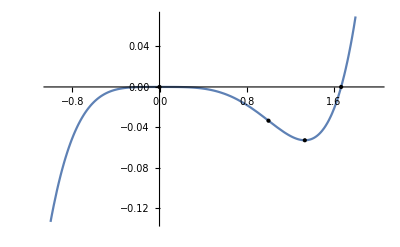

```mathematica
plotinator[-x^4/12+x^5/20,{x,-1,2}]
```

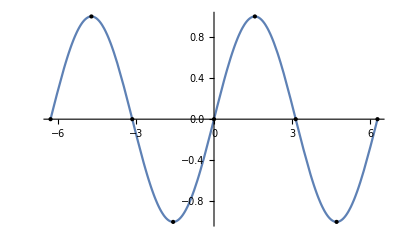

```mathematica
plotinator[Sin[x],{x,-2π,2π}]
```

```mathematica
ClearAll[obliqueAsymptote]
```

```mathematica
obliqueAsymptote[f_,x_]:=Module[{i,expandedForm,temp,output,hasOAsymptote},
expandedForm=Expand[f];
If[expandedForm[[0]]==Plus,
temp={};
output={};
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->-∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
output=DeleteDuplicates[output];
Return[output];
];
Return[{}];
];
```

```mathematica
valueOfInequality[inequ_,x_]:=Module[{},
If[inequ[[2]]==x,Return[inequ[[1]]]];
If[inequ[[1]]==x,Return[inequ[[2]]]];
]
```

```mathematica
verticleAsymptotes[f_,x_]:=Module[{i,j,dom,asymptotes,output},
dom=FunctionDomain[f,x];
asymptotes={};
output={};
For[i=1,i≤Length[dom],i++,
If[dom[[i,0]]==Less,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Greater,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Inequality,
For[j=1,j≤Length[dom[[i]]]-2,j=j+2,
AppendTo[asymptotes,valueOfInequality[dom[[i,j;;j+2]],x]];
];
];
];
asymptotes=DeleteDuplicates[asymptotes];
For[i=1,i≤Length[asymptotes],i++,
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
];
output=DeleteDuplicates[output];
Return[output];
];
```

```mathematica
horizontalAsymptotes[f_,x_]:=Module[{output,val},
output={};
val=0;
val=Limit[f,x->∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
val=Limit[f,x->-∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
output=DeleteDuplicates[output];
Return[output];
];
```

```mathematica
signToAscii[val_]:=Module[{},
If[val>0,Return["/"]];
If[val==0,Return["-"]];
If[val<0,Return["\\"]];
Return["Error"];
];
```

```mathematica
signTable[f_,x_,sdom_:True]:=Module[{i,j,TPs,xCordsOfTP,testedPoints,fDashVals},
TPs=DeleteDuplicates[turningPoints[f,x,sdom]];
If[Length[TPs]==0,Return["The function has no turning points"]];
xCordsOfTP={};
testedPoints={};
fDashVals={};
For[i=1,i≤Length[TPs],i++,
AppendTo[xCordsOfTP,TPs[[i,1]]];
];
If[Length[xCordsOfTP]==1,
Return[Grid[{Prepend[{xCordsOfTP[[1]]-1,xCordsOfTP[[1]],xCordsOfTP[[1]]+1},"x"],Prepend[D[f,x]/.x->{xCordsOfTP[[1]]-1,xCordsOfTP[[1]],xCordsOfTP[[1]]+1},"f'(x)"],Prepend[signToAscii/@(D[f,x]/.x->{xCordsOfTP[[1]]-1,xCordsOfTP[[1]],xCordsOfTP[[1]]+1}),"f'(x)"]},Frame->All]];
];
AppendTo[testedPoints,xCordsOfTP[[1]]-1];
For[i=1,i≤Length[xCordsOfTP]-1,i++,
AppendTo[testedPoints,(xCordsOfTP[[i]]+xCordsOfTP[[i+1]])/2];
];

testedPoints=Join[testedPoints,xCordsOfTP];
testedPoints=Sort[testedPoints];
AppendTo[testedPoints,xCordsOfTP[[i]]+1];
fDashVals=D[f,x]/.x->testedPoints;
j=1;
For[i=1,i≤Length[testedPoints],i++,
If[testedPoints[[i]]==xCordsOfTP[[j]],
fDashVals[[i]]=0;
j++;
If[j>Length[xCordsOfTP],Break[]];
];
];
Return[Grid[{Prepend[testedPoints,"x"],Prepend[fDashVals,"f'(x)"],Prepend[signToAscii/@fDashVals,"f'(x)"]},Frame->All]];
];
```

```mathematica
signTable[(x+1)^2(x-1.1),x]
```

x | -2. | -1. | -0.3 | 0.4 | 1.4
f'(x) | 7.2 | 0 | -1.47 | 0 | 7.2
f'(x) | / | - | \ | - | /

```mathematica
signTable[x^2,x]
```

x | -1 | 0 | 1
f'(x) | -2 | 0 | 2
f'(x) | \ | - | /

```mathematica
slopePointForm[y_,y1_,m_,x_,x1_]:=y==Collect[Solve[y-y1==m(x-x1),y],x][[1,1,2]]
```

```mathematica
slopePointForm[y,1,2,x,-1]
```

y==3+2 x